# Math 223: Homework 9

Ali Heydari

April. 8th, 2021

## Problem 1

Use second-order perturbation theory to find approximations to the roots of .

Since our problem is already in the perturbed form, we can use the perturbation theory and let 

x ∼ ∑_(n=0)^∞ x_n ϵ^n,   ϵ→0^+

Now we replace this in the original problem, and seek the roots using this expansion:

(∑_(n=0)^∞ x_n ϵ^n)^2+(∑_(n=0)^∞ x_n ϵ^n) + 6ϵ = 0.

so now we use Mathematica to solve this:

```mathematica
SeriesCoefficient[Series[(Sum[x[n] ϵ^n,{n,0,10}])^2+Sum[x[n] ϵ^n,{n,0,10}]+6ϵ,{ϵ,0,2}],0]
```

x[0]+x[0]^2

```mathematica
Solve[x[0]+x[0]^2==0,x[0]]
```

{{x[0]→-1},{x[0]→0}}

Now to find the higher order solutions for each one of the roots:

```mathematica
SeriesCoefficient[Series[(Sum[x[n] ϵ^n,{n,0,10}])^2+Sum[x[n] ϵ^n,{n,0,10}]+6ϵ,{ϵ,0,2}],1]/.x[0]->0
```

6+x[1]

```mathematica
Solve[6+x[1]==0,x[1]]
```

{{x[1]→-6}}

so that means that we have:



Now to find the higher order root:

```mathematica
SeriesCoefficient[Series[(Sum[x[n] ϵ^n,{n,0,10}])^2+Sum[x[n] ϵ^n,{n,0,10}]+6ϵ,{ϵ,0,2}],2]/.{x[0]->0,x[1]-> -6}
```

36+x[2]

```mathematica
Solve[36+x[2]==0,x[2]]
```

{{x[2]→-36}}

so we have the first root to be:

similarly for the other root:

```mathematica
SeriesCoefficient[Series[(Sum[x[n] ϵ^n,{n,0,10}])^2+Sum[x[n] ϵ^n,{n,0,10}]+6ϵ,{ϵ,0,2}],1]/.x[0]-> -1
```

6-x[1]

```mathematica
Solve[6-x[1]==0,x[1]]
```

{{x[1]→6}}

so we have the second root to be:

Now to go one order higher:

```mathematica
SeriesCoefficient[Series[(Sum[x[n] ϵ^n,{n,0,10}])^2+Sum[x[n] ϵ^n,{n,0,10}]+6ϵ,{ϵ,0,2}],2]/.{x[0]-> -1, x[1]-> 6}
```

36-x[2]

```mathematica
Solve[36-x[2]==0,x[2]]
```

{{x[2]→36}}

so we get the second solution to the second order to be:

## Problem 2

Compute all of the coefficients in the perturbation series solution to the initial-value problem 

 			,

Show that the series converges for all values of . Also, compute the perturbation series indirectly by
expanding the explicit exact solution in powers of .

We will try to find the solution in the limit as , and use the notion of perturbation expansion, that is we take:

y(x) ∼ ∑_(n=0)^∞ y_n(x) ϵ^n,   ϵ→0^+.

Now substituting the perturbation expansion in the ODE, we get:

(y_0'+ϵ y_1'+ϵ^2 y_2'+ϵ^3 y_3'+ ⋯)- (y_0+ϵ y_1+ϵ^2 y_2+ ⋯) - ϵx (y_0+ ϵ y_1+ ϵ^2 y_2+ ⋯)=0

to find the regular expression for the initial condition, we have:

(y_0(0)+y_1(0) + ϵ^2 y_2(0) + ⋯) = 1.

which allows us to construct a system of equations for specific orders. So to find the first order approximation to this perturbed system, we can solve for: 

O(1): y_0'-y_0=0, y_0(0) = 1.

```mathematica
DSolve[{Subscript[y, 0]'[x]-Subscript[y, 0][x]==0,Subscript[y, 0][0]==1},Subscript[y, 0][x],x]
```

{{y_0[x]→ⅇ^x}}

Next we find the order epsilon approximation:
O(ϵ): y_1'-y_1=xy_0, y_1(1) = 0.

```mathematica
DSolve[{Subscript[y, 1]'[x]- Subscript[y, 1][x] ==x ⅇ^x,Subscript[y, 1][0]==0},Subscript[y, 1][x],x]
```

{{y_1[x]→(ⅇ^x x^2)/2}}

therefore we can write the asymptotic approximation as: 


Now to check the validity of our solution:

```mathematica
DSolve[{y'[x]- y[x]-ϵ*x*y[x] == 0,y[0]==1},y[x],x]
```

{{y[x]→ⅇ^(x+(x^2 ϵ)/2)}}

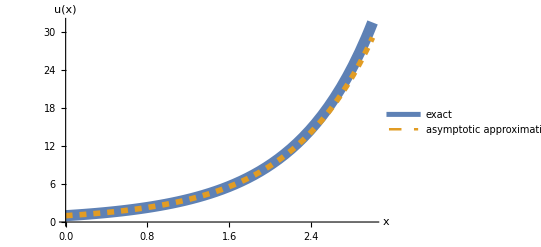

```mathematica
Plot[{ⅇ^(x+(x^2 ϵ)/2)/.ϵ->0.1,ⅇ^x+ϵ *1/2*ⅇ^x*x^2/.ϵ->0.1},{x,0,3},PlotStyle-> {Directive[Solid,Thickness[0.02]], Directive[Dashed,Thickness[0.01]]},AxesLabel->{Style["x",Italic,18],Style["u(x)", Italic, 18]}, TicksStyle->Directive[FontSize->14],PlotLegends->{"exact","asymptotic approximation"}]
```

Our approximation seems very descent, given that we have only calculated the approximation up to first order! So this concludes finding the solution in perturbed powers of ϵ.

## Problem 3

Show that the solution to the initial-value problem

 			,

remains bounded for all real . Obtain a first-order perturbative approximation to  and and show that it is unbounded as . Conclude that the first order approximation of is valid only for .